Polinomio de Lagrange

### Autores : Helver Jussef López Abril Michael Velasquez Rico

Este programa calcula el polinomio de interpolación de Lagrange para tres puntos y muestra su grafica :

```mathematica
f[x_]=1/x;
```

```mathematica
Subscript[L, 0][x_]:=((Subscript[x, 0]-Subscript[x, 1])*(x-Subscript[x, 2]))/((Subscript[x, 0]-Subscript[x, 1])*(Subscript[x, 0]-Subscript[x, 2]));
```

```mathematica
Subscript[L, 1][x_]:=((x-Subscript[x, 0])*(x-Subscript[x, 2]))/((Subscript[x, 1]-Subscript[x, 0])*(Subscript[x, 1]-Subscript[x, 2]));    
Subscript[L, 2][x_]:=((x-Subscript[x, 0])*(x-Subscript[x, 1]))/((Subscript[x, 2]-Subscript[x, 0])*(Subscript[x, 2]-Subscript[x, 1]));
```

```mathematica
Subscript[x, 0]=2; 
Subscript[x, 1]=2.5;
Subscript[x, 2]=4;
```

```mathematica
Subscript[L, 0][x]
```

-0.5 (-4+x)

```mathematica
Subscript[L, 1][x]
```

-1.33333 (-4+x) (-2+x)

```mathematica
Subscript[L, 2][x]
```

0.333333 (-2.5+x) (-2+x)

```mathematica
f[Subscript[x, 0]]
```

1/2

```mathematica
f[Subscript[x, 1]]
```

0.4

```mathematica
f[Subscript[x, 2]]
```

1/4

```mathematica
Subscript[P, 2][x]= f[Subscript[x, 0]]*Subscript[L, 0][x]+f[Subscript[x, 1]]Subscript[L, 1][x]+f[Subscript[x, 2]]Subscript[L, 2][x]
```

-0.25 (-4+x)-0.533333 (-4+x) (-2+x)+0.0833333 (-2.5+x) (-2+x)

```mathematica
-0.25 (-4+3)-0.5 (-4+3) (-2+3)+0.083 (-2.5`+3) (-2+3)
```

0.5425

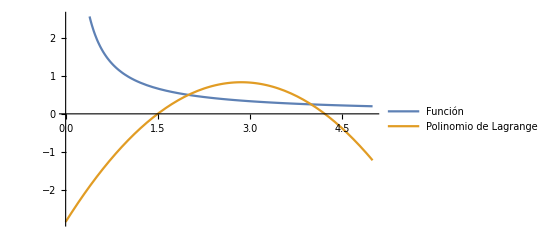

```mathematica
Plot[{f[x],-0.25 (-4+x)-0.5333333333333333 (-4+x) (-2+x)+0.08333333333333333 (-2.5+x) (-2+x)},{x,0,5},PlotLegends->LineLegend[{"Función","Polinomio de Lagrange"},LegendFunction->Frame]]
```